```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\tonyr\OneDrive - UW\School Stuff\2020 Winter\MATH 381\MATH-381-Project-2

```mathematica
session = StartExternalSession["Python"]
```

ExternalSessionObject[…]

```mathematica
ExternalEvaluate[session, File["bigramAddk.py"]];
result = %;
words = Last[result];
transitionMatrix = Normal[First[result]];
indStart = Position[words,"::START::"][[1]][[1]];
```

DiscreteMarkovProcess::dmnorm: The transition matrix had some row sums that were not 1, so those rows have been adjusted by dividing by the row sum or by setting the diagonal element to 1.

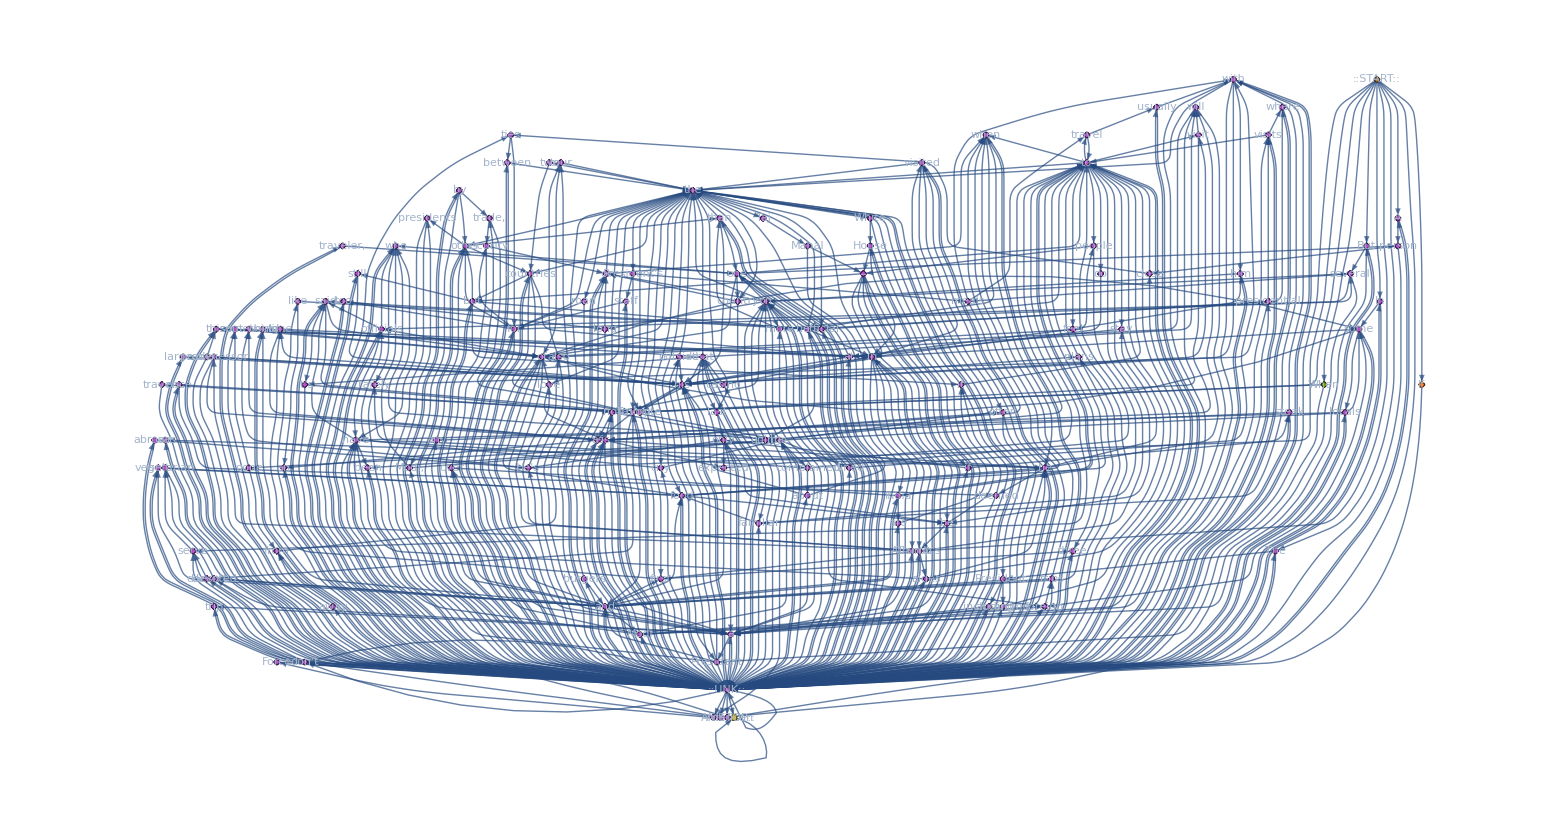

```mathematica
g=Magnify[Graph[
DiscreteMarkovProcess[indStart, transitionMatrix], VertexLabels->MapIndexed[First[#2]->Placed[#1, Center]&,words],
GraphLayout->{"LayeredDigraphEmbedding", "RootVertex"->indStart},
AspectRatio->1/2, ImageSize->8000
],0.2]
Export["graph.svg",g];
```